prog1

```mathematica
n=31;
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
a=Flatten[Import["out.txt","Table"]];
xh=a[[;;n]];
fo = a[[n+1;;]];
```

```mathematica
xsli={1,Floor[n/2.] + 1,n};
fsl = {0.01,0.05,1.5};
```

```mathematica
ner=Nearest[fo,fsl[[3]]]
Position[fo,ner[[1]]][[1,1]]
```

{0.4995}

1000

```mathematica
b=Partition[Flatten[Import["temp.txt", "Table"]],n];
```

```mathematica
Dimensions[b]
```

{1000,31}

```mathematica
tx=b[[;;,#]]&/@xsli;
tx={fo, #}ᵀ&/@tx;
```

```mathematica
tx[[1]]//Length
```

1000

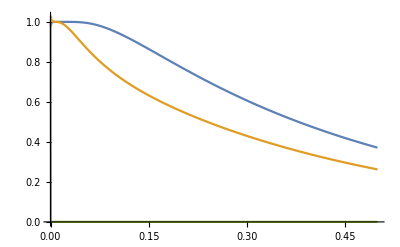

```mathematica
ListPlot[tx,Joined->True]
```

```mathematica
b//MatrixForm;
```

prog2

```mathematica
n=41;
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
a=Flatten[Import["out.txt","Table"]];
xh=a[[;;n]];
fo = a[[n+1;;]];
```

```mathematica
xsli={1,Floor[n/2.] + 1,n};
fsl = {0.01,0.05,1.5};
```

```mathematica
ner=Nearest[fo,fsl[[3]]]
Position[fo,ner[[1]]][[1,1]]
```

{0.499844}

3200

```mathematica
b=Partition[Flatten[Import["temp.txt", "Table"]],n];
```

```mathematica
Dimensions[b]
```

{3200,41}

```mathematica
tx=b[[;;,#]]&/@xsli;
tx={fo, #}ᵀ&/@tx;
```

```mathematica
tx[[1]]//Length
```

3200

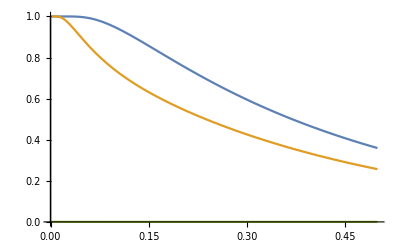

```mathematica
ListPlot[tx,Joined->True]
```

```mathematica
b//MatrixForm;
```

```mathematica
tx[[3]]
```

{{0.,1.},{0.00015625,0.000537892},{0.0003125,0.000403492},{0.00046875,0.000336273},{0.000625,0.000294255},3191,{0.499375,7.70193×10^-6},{0.499531,7.69888×10^-6},{0.499688,7.69584×10^-6},{0.499844,7.69279×10^-6}}
 |  |  |  |